Exercises for Section 29 | More about Pure Functions

Use Prime and Array to generate a list of the first 100 primes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

Use Prime and Array to find successive differences between the first 100 primes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Array[Prime-#,100]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[Prime-#1,100&].

Array[Prime-#1,100&]

```mathematica
Table[Prime[n+1]-Prime[n],{n,99}]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

```mathematica
Array[Prime+1,100]
```

{(1+Prime)[1],(1+Prime)[2],(1+Prime)[3],(1+Prime)[4],(1+Prime)[5],(1+Prime)[6],(1+Prime)[7],(1+Prime)[8],(1+Prime)[9],(1+Prime)[10],(1+Prime)[11],(1+Prime)[12],(1+Prime)[13],(1+Prime)[14],(1+Prime)[15],(1+Prime)[16],(1+Prime)[17],(1+Prime)[18],(1+Prime)[19],(1+Prime)[20],(1+Prime)[21],(1+Prime)[22],(1+Prime)[23],(1+Prime)[24],(1+Prime)[25],(1+Prime)[26],(1+Prime)[27],(1+Prime)[28],(1+Prime)[29],(1+Prime)[30],(1+Prime)[31],(1+Prime)[32],(1+Prime)[33],(1+Prime)[34],(1+Prime)[35],(1+Prime)[36],(1+Prime)[37],(1+Prime)[38],(1+Prime)[39],(1+Prime)[40],(1+Prime)[41],(1+Prime)[42],(1+Prime)[43],(1+Prime)[44],(1+Prime)[45],(1+Prime)[46],(1+Prime)[47],(1+Prime)[48],(1+Prime)[49],(1+Prime)[50],(1+Prime)[51],(1+Prime)[52],(1+Prime)[53],(1+Prime)[54],(1+Prime)[55],(1+Prime)[56],(1+Prime)[57],(1+Prime)[58],(1+Prime)[59],(1+Prime)[60],(1+Prime)[61],(1+Prime)[62],(1+Prime)[63],(1+Prime)[64],(1+Prime)[65],(1+Prime)[66],(1+Prime)[67],(1+Prime)[68],(1+Prime)[69],(1+Prime)[70],(1+Prime)[71],(1+Prime)[72],(1+Prime)[73],(1+Prime)[74],(1+Prime)[75],(1+Prime)[76],(1+Prime)[77],(1+Prime)[78],(1+Prime)[79],(1+Prime)[80],(1+Prime)[81],(1+Prime)[82],(1+Prime)[83],(1+Prime)[84],(1+Prime)[85],(1+Prime)[86],(1+Prime)[87],(1+Prime)[88],(1+Prime)[89],(1+Prime)[90],(1+Prime)[91],(1+Prime)[92],(1+Prime)[93],(1+Prime)[94],(1+Prime)[95],(1+Prime)[96],(1+Prime)[97],(1+Prime)[98],(1+Prime)[99],(1+Prime)[100]}

```mathematica
Array[Prime[#+1]-Prime[#]&,99]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

Use Array and Grid to make a 10 by 10 addition table. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Array[Plus,{10,10}]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

Use FoldList, Times and Range to successively multiply numbers up to 10 (making factorials). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FoldList[Times,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

Use FoldList and Array to compute the successive products of the first 10 primes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FoldList[Times[]]
```

```mathematica
Array[FoldList[Prime[#]*Prime[#]]&,10]
```

{FoldList[4],FoldList[9],FoldList[25],FoldList[49],FoldList[121],FoldList[169],FoldList[289],FoldList[361],FoldList[529],FoldList[841]}

```mathematica
Array[FoldList[Times,1,{1,2}],1,10]
```

{{1,1,2}[10]}

```mathematica
FoldList[Prime#,0,Range[10]]&
```

FoldList[Prime #1,0,Range[10]]&

```mathematica
Array[Prime[#]*Prime[#]&,0]
```

{}

```mathematica
FoldList[Times,1,Array[Prime,10]]
```

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

Use FoldList to successively ImageAdd regular polygons with between 3 and 8 sides, and with opacity 0.2. |

EXPECTED OUTPUT »

-Graphics- | ×

ImageAdd::bdarg: Expecting a number, image, or graphics instead of ()[1].

ImageAdd::imginv: Expecting an image or graphics instead of ImageAdd[,()[1]].

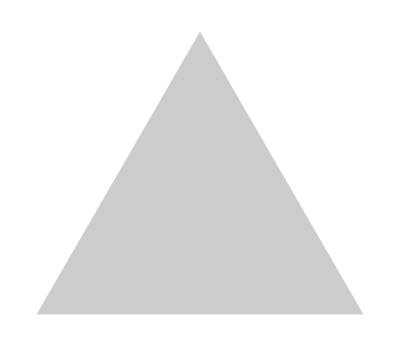
{-Graphics-,ImageAdd[-Graphics-,(-Graphics-)[1]],ImageAdd[ImageAdd[-Graphics-,(-Graphics-)[1]],(-Graphics-)[2]]}

```mathematica
FoldList[ImageAdd,Graphics[{Opacity[0.2],RegularPolygon[3]}],Array[Graphics[{Opacity[0.2],RegularPolygon[n]}],2]]
```

```mathematica
FoldList[ImageAdd,Table[Graphics[{Opacity[0.2],RegularPolygon[i]}],{i,3,8}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use Array to make a 10 by 10 grid where the leading diagonal and everything below it is 1 and the rest is 0. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Array[x,{10,10}]//Grid
```

x[1,1] | x[1,2] | x[1,3] | x[1,4] | x[1,5] | x[1,6] | x[1,7] | x[1,8] | x[1,9] | x[1,10]
x[2,1] | x[2,2] | x[2,3] | x[2,4] | x[2,5] | x[2,6] | x[2,7] | x[2,8] | x[2,9] | x[2,10]
x[3,1] | x[3,2] | x[3,3] | x[3,4] | x[3,5] | x[3,6] | x[3,7] | x[3,8] | x[3,9] | x[3,10]
x[4,1] | x[4,2] | x[4,3] | x[4,4] | x[4,5] | x[4,6] | x[4,7] | x[4,8] | x[4,9] | x[4,10]
x[5,1] | x[5,2] | x[5,3] | x[5,4] | x[5,5] | x[5,6] | x[5,7] | x[5,8] | x[5,9] | x[5,10]
x[6,1] | x[6,2] | x[6,3] | x[6,4] | x[6,5] | x[6,6] | x[6,7] | x[6,8] | x[6,9] | x[6,10]
x[7,1] | x[7,2] | x[7,3] | x[7,4] | x[7,5] | x[7,6] | x[7,7] | x[7,8] | x[7,9] | x[7,10]
x[8,1] | x[8,2] | x[8,3] | x[8,4] | x[8,5] | x[8,6] | x[8,7] | x[8,8] | x[8,9] | x[8,10]
x[9,1] | x[9,2] | x[9,3] | x[9,4] | x[9,5] | x[9,6] | x[9,7] | x[9,8] | x[9,9] | x[9,10]
x[10,1] | x[10,2] | x[10,3] | x[10,4] | x[10,5] | x[10,6] | x[10,7] | x[10,8] | x[10,9] | x[10,10]

```mathematica
Array[#1*#2 &, {5, 5}] // Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

```mathematica
Grid@Table[Table[x,10],10]
```

x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x
x | x | x | x | x | x | x | x | x | x

```mathematica
Array[If[#1≥#2,1,0]&,{10,10}]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1